{{i→0.557146}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{vd→0.442854}}

{{vd→0.442854}}

{{1-(vd→0.442854)}}

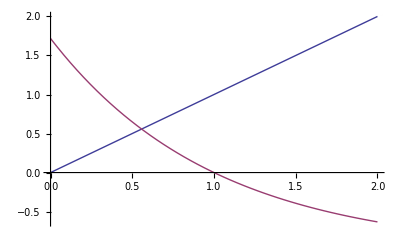

```mathematica
ClearAll["Global`*"]
vs=1;
r=1;
i0=1;
nvt=1;
NSolve[{i == i0*(Exp[(vs-i*r)/nvt]-1)},i,Reals]
vd0= NSolve[vd == nvt*Log[1 + ((vs-vd)/(i0*r))],vd]
vd0
(vs-vd0)/r
Plot[{x,i0*(Exp[(vs-x*r)/nvt])-1},{x,0,2}]
```

```mathematica
vd/.{{vd->0.4428544010023886}}
```

{0.442854}

```mathematica
First[{0.4428544010023886}]
```

0.442854